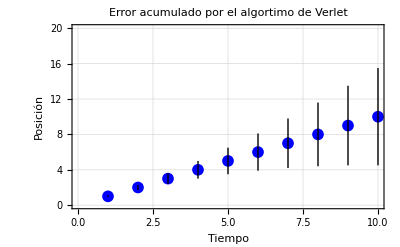

```mathematica
(*Parámetros de la simulación*)tmax=10; (*Tiempo máximo de simulación*)
dt=1; (*Paso de tiempo,para simplificar*)
tiempos=Range[1,tmax,dt]; (*Lista de tiempos discretos*)

(*Posición teórica,que en este caso es solo un valor arbitrario*)
posicionTeorica[t_]:=t  (*Suponemos que la posición es lineal con el tiempo*)

(*Calcular los errores acumulados en cada paso n*)
errores=(tiempos*(tiempos+1))/2;

(*Generar las posiciones con barras de error acumulado*)
datosConError=Transpose[{tiempos,posicionTeorica/@tiempos,errores}];

(*Graficar las posiciones con barras de error acumulado*)
ListPlot[datosConError[[All,{1,2}]],PlotRange->{{0,tmax},{0,20}},(*Limitar el rango de la gráfica para alejarla*)PlotStyle->Blue,PlotMarkers->{Automatic,12},PlotLabel->"Error acumulado por el algortimo de Verlet",AxesLabel->{"Tiempo","Posición"},Epilog->{(*Agregar barras de error verticales para cada punto con un factor de reducción*)Table[Line[{{tiempos[[i]],posicionTeorica[tiempos[[i]]]-errores[[i]]/10},{tiempos[[i]],posicionTeorica[tiempos[[i]]]+errores[[i]]/10}}],{i,Length[tiempos]}]},PlotTheme->"Detailed"]
```